```mathematica
ClearAll["Global`*"];
```

```mathematica
coords = {t,r,θ,ϕ};
n=Length[coords];
rplus = M+Sqrt[M^2-a^2];
tt=2 M r/ρ-1;
rr=ρ/Δ;
θθ=ρ;
ϕϕ=(Δ+(2 M r (r^2+a^2))/ρ)Sin[θ]^2;
tϕ=-4 a M r Sin[θ]^2/ρ;
metric={{tt,0,0,tϕ},{0,rr,0,0},{0,0,θθ,0},{tϕ,0,0,ϕϕ}};
metric//MatrixForm;
inversemetric=Simplify[Inverse[metric]];
inversemetric //MatrixForm;
```

```mathematica
a=.;M=.;
ρ=r^2+a^2 Cos[θ]^2;
Δ=r^2 - 2 M r+ a^2;
christoffel:=christoffel=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*
(D[metric[[s,j]],coords[[k]] ]+
D[metric[[s,k]],coords[[j]] ]-D[metric[[j,k]],coords[[s]] ]),{s,1,n}],
{i,1,n},{j,1,n},{k,1,n}] ]
listchristoffel:=Table[If[UnsameQ[christoffel[[i,j,k]],0],{ToString[Γ[i,j,k]],christoffel[[i,j,k]]}] ,{i,1,n},{j,1,n},{k,1,j}]
geodesic:=geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]]coords[[j]]' coords[[k]]',{j,1,n},
{k,1,n}],{i,1,n}]]
listgeodesic:=Table[{"d/dτ"ToString[coords[[i]]'],"=",geodesic[[i]]},{i,1,n}]
geodesic:=geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]]coords[[j]]' coords[[k]]',{j,1,n},
{k,1,n}],{i,1,n}]]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listchristoffel],Null],2],TableSpacing->{2,2}]
TableForm[Partition[DeleteCases[Flatten[listgeodesic],Null],2],TableSpacing->{2,2}]
```

Γ[1, 2, 1] | -(M (a^2-2 r^2+a^2 Cos[2 θ]) (a^4+2 r^4+3 a^2 r (-2 M+r)+a^2 (a^2+r (6 M+r)) Cos[2 θ]))/(4 (r^2+a^2 Cos[θ]^2) (2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4+r^2 (r^3 (-2 M+r)+a^2 (4 M^2+r^2)-8 a^2 M^2 Cos[2 θ])))
Γ[1, 3, 1] | -(a^2 M r Cos[θ] (a^4+2 r^3 (-8 M+r)+a^2 r (-14 M+3 r)+a^2 (a^2+r (-2 M+r)) Cos[2 θ]) Sin[θ])/((r^2+a^2 Cos[θ]^2) (2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4+r^2 (r^3 (-2 M+r)+a^2 (4 M^2+r^2)-8 a^2 M^2 Cos[2 θ])))
Γ[1, 4, 2] | (2 a M (-r^2 (a^2+3 r^2)+a^2 (a^2-r^2) Cos[θ]^2) Sin[θ]^2)/(2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4+r^2 (r^3 (-2 M+r)+a^2 (4 M^2+r^2)-8 a^2 M^2 Cos[2 θ]))
Γ[1, 4, 3] | (4 a^3 M r (a^2+r (-2 M+r)) Cos[θ] Sin[θ]^3)/(2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4+r^2 (r^3 (-2 M+r)+a^2 (4 M^2+r^2)-8 a^2 M^2 Cos[2 θ]))
Γ[2, 1, 1] | -(M (a^2+r (-2 M+r)) (-r^2+a^2 Cos[θ]^2))/((r^2+a^2 Cos[θ]^2)^3)
Γ[2, 2, 2] | (r (a^2-M r)+a^2 (M-r) Cos[θ]^2)/((a^2+r (-2 M+r)) (r^2+a^2 Cos[θ]^2))
Γ[2, 3, 2] | -(a^2 Cos[θ] Sin[θ])/(r^2+a^2 Cos[θ]^2)
Γ[2, 3, 3] | -(r (a^2+r (-2 M+r)))/(r^2+a^2 Cos[θ]^2)
Γ[2, 4, 1] | (2 a M (a^2+r (-2 M+r)) (-r^2+a^2 Cos[θ]^2) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)^3)
Γ[2, 4, 4] | ((a^2+r (-2 M+r)) (a^2 M r^2-r^5-a^2 (a^2 M+r^2 (M+2 r)) Cos[θ]^2+a^4 (M-r) Cos[θ]^4) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)^3)
Γ[3, 1, 1] | -(2 a^2 M r Cos[θ] Sin[θ])/((r^2+a^2 Cos[θ]^2)^3)
Γ[3, 2, 2] | (a^2 Cos[θ] Sin[θ])/((a^2+r (-2 M+r)) (r^2+a^2 Cos[θ]^2))
Γ[3, 3, 2] | r/(r^2+a^2 Cos[θ]^2)
Γ[3, 3, 3] | -(a^2 Cos[θ] Sin[θ])/(r^2+a^2 Cos[θ]^2)
Γ[3, 4, 1] | (2 a M r (a^2+r^2) Sin[2 θ])/((r^2+a^2 Cos[θ]^2)^3)
Γ[3, 4, 4] | -(Cos[θ] Sin[θ] (a^2-2 M r+r^2+(2 M r (a^2+r^2))/(r^2+a^2 Cos[θ]^2)+(2 a^2 M r (a^2+r^2) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)^2)))/(r^2+a^2 Cos[θ]^2)
Γ[4, 2, 1] | (2 a M (r^2-a^2 Cos[θ]^2))/(2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4+r^2 (r^3 (-2 M+r)+a^2 (4 M^2+r^2)-8 a^2 M^2 Cos[2 θ]))
Γ[4, 3, 1] | -(2 a M r (a^2+r (-2 M+r)) (a^2+2 r^2+a^2 Cos[2 θ]) Cot[θ])/((r^2+a^2 Cos[θ]^2) (2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4+r^2 (r^3 (-2 M+r)+a^2 (4 M^2+r^2)-8 a^2 M^2 Cos[2 θ])))
Γ[4, 4, 2] | (2 a^2 M^2 r^3-a^2 M r^4-2 M r^6+r^7-a^2 r (2 a^2 M^2+r^2 (2 M^2+3 M r-3 r^2)) Cos[θ]^2+a^4 (a^2 M+r (2 M^2-2 M r+3 r^2)) Cos[θ]^4-a^6 (M-r) Cos[θ]^6-8 a^2 M^2 r^3 Sin[θ]^2+2 a^4 M^2 r Sin[2 θ]^2)/((r^2+a^2 Cos[θ]^2) (2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4+r^2 (r^3 (-2 M+r)+a^2 (4 M^2+r^2)-8 a^2 M^2 Cos[2 θ])))
Γ[4, 4, 3] | (Cos[θ] (a^2 r^2 (a^2 (-4 M^2+3 r^2)+r^2 (4 M^2-6 M r+3 r^2)) Cos[θ] Cot[θ]+a^4 r^2 (3 a^2+4 M^2-6 M r+3 r^2) Cos[θ]^3 Cot[θ]+a^6 (a^2+r (-2 M+r)) Cos[θ]^5 Cot[θ]+2 a^4 M r (a^2+r (8 M+r)) Cos[θ]^2 Sin[θ]+r^2 (-(2 M-r) r^2 (r^3+a^2 (2 M+r)) Csc[θ]+2 a^2 M (a^2 (2 M+r)+r^2 (6 M+r)-4 a^2 M Cos[2 θ]) Sin[θ])))/((r^2+a^2 Cos[θ]^2) (2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4+r^2 (r^3 (-2 M+r)+a^2 (4 M^2+r^2)-8 a^2 M^2 Cos[2 θ])))

d/dτ t' | =
(M (a^2 r θ' (2 (a^4+2 r^3 (-8 M+r)+a^2 r (-14 M+3 r)+a^2 (a^2+r (-2 M+r)) Cos[2 θ]) Sin[2 θ] t'-8 a (a^2+r (-2 M+r)) Cos[θ] (a^2+2 r^2+a^2 Cos[2 θ]) Sin[θ]^3 ϕ')+r' ((a^2-2 r^2+a^2 Cos[2 θ]) (a^4+2 r^4+3 a^2 r (-2 M+r)+a^2 (a^2+r (6 M+r)) Cos[2 θ]) t'+8 a ((r^4 (a^2+3 r^2)+(-a^6+a^4 r^2) Cos[θ]^4) Sin[θ]^2+a^2 r^4 Sin[2 θ]^2) ϕ')))/(2 (r^2+a^2 Cos[θ]^2) (2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4+r^2 (r^3 (-2 M+r)+a^2 (4 M^2+r^2)-8 a^2 M^2 Cos[2 θ]))) | d/dτ r'
= | (-((r^2+a^2 Cos[θ]^2)^2 (r (a^2-M r)+a^2 (M-r) Cos[θ]^2) (r')^2)/(a^2+r (-2 M+r))+M (a^2+r (-2 M+r)) (-r^2+a^2 Cos[θ]^2) (t')^2+2 a^2 Cos[θ] (r^2+a^2 Cos[θ]^2)^2 Sin[θ] r' θ'+r (a^2+r (-2 M+r)) (r^2+a^2 Cos[θ]^2)^2 (θ')^2-4 a M (a^2+r (-2 M+r)) (-r^2+a^2 Cos[θ]^2) Sin[θ]^2 t' ϕ'-(a^2+r (-2 M+r)) (a^2 M r^2-r^5-a^2 (a^2 M+r^2 (M+2 r)) Cos[θ]^2+a^4 (M-r) Cos[θ]^4) Sin[θ]^2 (ϕ')^2)/((r^2+a^2 Cos[θ]^2)^3)
d/dτ θ' | =
(-(a^2 Cos[θ] (r^2+a^2 Cos[θ]^2)^2 Sin[θ] (r')^2)/(a^2+r (-2 M+r))+a^2 M r Sin[2 θ] (t')^2-2 r (r^2+a^2 Cos[θ]^2)^2 r' θ'+a^2 Cos[θ] (r^2+a^2 Cos[θ]^2)^2 Sin[θ] (θ')^2-4 a M r (a^2+r^2) Sin[2 θ] t' ϕ'+Cos[θ] (r^2+a^2 Cos[θ]^2)^2 Sin[θ] (a^2-2 M r+r^2+(2 M r (a^2+r^2))/(r^2+a^2 Cos[θ]^2)+(2 a^2 M r (a^2+r^2) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)^2)) (ϕ')^2)/((r^2+a^2 Cos[θ]^2)^3) | d/dτ ϕ'
= | -(2 (θ' (-2 a M r (a^2+r (-2 M+r)) (a^2+2 r^2+a^2 Cos[2 θ]) Cot[θ] t'+((r^2+a^2 Cos[θ]^2) (-(2 M-r) r^2 (r^3+a^2 (2 M+r))+2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4) Cot[θ]+1/2 a^2 M r (a^2+r^2) (a^2+2 r (6 M+r)+a^2 Cos[2 θ]) Sin[2 θ]) ϕ')+r' (2 a M (r^4-a^4 Cos[θ]^4) t'+(2 a^2 M^2 r^3-a^2 M r^4-2 M r^6+r^7-a^2 r (2 a^2 M^2+2 M^2 r^2+3 M r^3-3 r^4) Cos[θ]^2+a^4 (a^2 M+2 M^2 r-2 M r^2+3 r^3) Cos[θ]^4-a^6 (M-r) Cos[θ]^6-8 a^2 M^2 r^3 Sin[θ]^2+2 a^4 M^2 r Sin[2 θ]^2) ϕ')))/((r^2+a^2 Cos[θ]^2) (2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4+r^2 (r^3 (-2 M+r)+a^2 (4 M^2+r^2)-8 a^2 M^2 Cos[2 θ])))

```mathematica
uinvar=0;M=1;a=0.9; τval=28; rplus = M+Sqrt[M^2-a^2]; τend = .;
ivs = {-0.15,0.0,0.005}; ics = {0,5,π/2,π/4};
ivs=Join[{χ},ivs];
tmp=metric;
tmp=tmp/.Table[coords[[i]]->ics[[i]],{i,0,n}];
tmp=ivs.(tmp.ivs);
χslv=Solve[tmp==uinvar,χ];
ivs[[1]]=Last[χ/.χslv];
deq=Table[coords[[i]]''[τ]==(geodesic[[i]]/.Join[Table[coords[[i]]'->coords[[i]]'[τ],{i,1,n}],Table[coords[[i]]->coords[[i]][τ],{i,1,n}]]),{i,1,n}];
deq=Join[deq,Table[coords[[i]]'[0]==ivs[[i]],{i,1,n}],Table[coords[[i]][0]==ics[[i]],{i,1,n}]];
soln=NDSolve[deq,coords,{τ,0,τval},
Method->{"EventLocator","Event":>(r[τ]≤1.1*rplus),"EventAction":>Throw[τend=τ,"StopIntegration"]}];
(*Method->{"EventLocator","Event":>(r[τ]<1.1*rplus),
"EventAction":>Print["event horizon crossed at r=",r[τ]," with rplus=",rplus," when τ=",τ]}];*)
τend
```

27.6809

27.6809

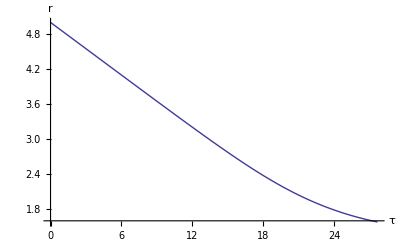

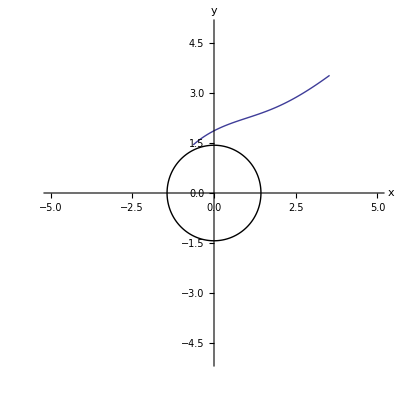

```mathematica
sphslnToCartsln[soln_]:=Block[{xs,ys,zs},xs=r[τ] Sin[θ[τ]] Cos[ϕ[τ]]/.soln ;ys=r[τ] Sin[θ[τ]] Sin[ϕ[τ]]/.soln;zs=r[τ] Cos[θ[τ]]/.soln;{xs,ys,zs}]
τplot = τend
it = soln[[1]][[1]][[2]]; it[τplot];
ir = soln[[1]][[2]][[2]]; ir[τplot];
iθ = soln[[1]][[3]][[2]]; iθ[τplot];
iϕ = soln[[1]][[4]][[2]]; iϕ[τplot];
xyz=sphslnToCartsln[soln];
Plot[Evaluate[coords[[2]][τ]/.soln],{τ,0,τplot},AxesLabel->{"τ","r"}]
horizpl=PolarPlot[rplus,{θ,0,2 Pi},DisplayFunction->Identity,PlotStyle->{Black,Thick}];
ParametricPlot[Evaluate[{xyz[[1]],xyz[[2]]}//Flatten],{τ,0,τplot},DisplayFunction->Identity];
Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-5,5},{-5,5}}]
```

```mathematica
soln[[1]][[2]][[2]][1.4358898943540672]
rplus
soln[[1]][[2]][[2]][1]<rplus
coords[[2]][5] /. soln[[1]][[2]]
coords[[2]][5]
soln[[1]][[2]]
```

4.78456

1.43589

False

4.24951

r[5]

r→InterpolatingFunction[{{0.,28.}},<>]